# Parameter Inference with SDE models

## “Good results” with synthetic data (polymer figure for paper here)

## Sin rain, n = 10, j = 10, nnapa = 3, dτ = 0.3

## Preliminaries

### Directories, packages, filenames

```mathematica
SetDirectory["C:/Users/ulzegasi/Julia_files/ParInf_HMC/good_results/n10 j10"]
inputdir="C:/Users/ulzegasi/Julia_files/ParInf_HMC/input_data";
Needs["CustomTicks`"]
Needs["ErrorBarPlots`"]
fname="_sinr800_120_130";
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC\good_results\n10 j10

### Loading parameters and data

```mathematica
qstemp=Import["last_qs"<>fname<>".dat"];
qs=Table[qstemp[[i,1]],{i,1,Length[qstemp]}];

predy=Import["predy"<>fname<>".dat"];
predq=Import["predq"<>fname<>".dat"];

thetas=Import["thetas"<>fname<>".dat"];

energiestemp=Import["energies"<>fname<>".dat"];
energies=Table[energiestemp[[i,1]],{i,1,Length[energiestemp]}];

paramlist=Import["params"<>fname<>".dat"];

reject=Import["reject"<>fname<>".dat"];
```

```mathematica
Nd=paramlist[[Position[paramlist,"N"][[1,1]],2]];
j=paramlist[[Position[paramlist,"j"][[1,1]],2]];
n=paramlist[[Position[paramlist,"n"][[1,1]],2]];
dt=paramlist[[Position[paramlist,"dt"][[1,1]],2]];

t=Table[0,{i,1,Nd}];
t[[1]]=paramlist[[Position[paramlist,"t[1]"][[1,1]],2]];
Do[t[[i]]=t[[i-1]]+dt,{i,2,Nd}];

T=dt*(Nd-1);

nparams=paramlist[[Position[paramlist,"nparams"][[1,1]],2]];
trueK=paramlist[[Position[paramlist,"true_K"][[1,1]],2]];
trueg=paramlist[[Position[paramlist,"true_gam"][[1,1]],2]];
sigma=paramlist[[Position[paramlist,"sigma"][[1,1]],2]];
K=paramlist[[Position[paramlist,"K"][[1,1]],2]];
gamma=paramlist[[Position[paramlist,"gam"][[1,1]],2]];

nsburnin=paramlist[[Position[paramlist,"nsample_burnin"][[1,1]],2]];
nseff=paramlist[[Position[paramlist,"nsample_eff"][[1,1]],2]];
nsample=nsburnin+nseff;

Mbdyburnin=paramlist[[Position[paramlist,"m_bdy_burnin"][[1,1]],2]];
Mbdy=paramlist[[Position[paramlist,"m_bdy"][[1,1]],2]];
Mthetaburnin=paramlist[[Position[paramlist,"m_theta_burnin"][[1,1]],2]];
Mtheta={paramlist[[Position[paramlist,"m_theta_bet"][[1,1]],2]],paramlist[[Position[paramlist,"m_theta_gam"][[1,1]],2]]};
Mstageburnin=paramlist[[Position[paramlist,"m_stg_burnin"][[1,1]],2]];


Mstage=paramlist[[Position[paramlist,"m_stg"][[1,1]],2]];

dtau=paramlist[[Position[paramlist,"dtau"][[1,1]],2]];
nnapa=paramlist[[Position[paramlist,"n_napa"][[1,1]],2]];

bet=Sqrt[T*thetas[[All,2]]/thetas[[All,1]]];
```

```mathematica
ty=Round[Array[#&,n+1,{1,Nd}]];
```

```mathematica
iodata=Import["iodata"<>fname<>".dat"];
(*S=Table[iodata[[i,1]],{i,2,Nd+1}];*)
r=Table[iodata[[i,1]],{i,Nd+3,2*Nd+2}]; 
y=Table[iodata[[i,1]],{i,2*Nd+4,Length[iodata]}];

St=Import[inputdir<>"/St_n10_K50_g02_s10_sinr.dat"];
S=St[[All,1]];
tS=St[[All,2]];
```

```mathematica
uchains raw=Import["u_chains"<>fname<>".dat"];
u1=Round[uchains raw[[1,1]]];
u2=Round[uchains raw[[1,2]]];
u3=Round[uchains raw[[1,3]]];
u4=Round[uchains raw[[1,4]]];
uchains=uchains raw[[Range[2,Length[uchains raw]],All]];
```

## Plots

### Polymer

```mathematica
Dimensions[predq[[1]]]
```

{101}

```mathematica
(*PlotMarkers->Graphics[{Black,Thick,Circle[]},ImageSize->9],*)
```

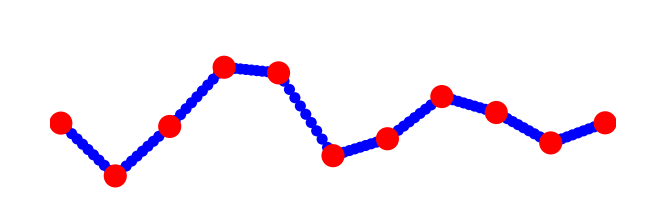

```mathematica
poly1=Show[
ListPlot[predq[[1]],PlotStyle->{RGBColor[0,0,1],PointSize[0.012]},Joined->True],
ListPlot[predq[[1]],PlotStyle->{RGBColor[0,0,1],PointSize[0.012]},Joined->False],
ListPlot[Transpose[{ty,predq[[1,ty]]}],PlotStyle->{RGBColor[1,0,0],PointSize[0.025]},Joined->False],
AspectRatio->1/3,
Axes->False,
PlotRange->{All,{-0.7,1.05}},Background->None
]
```

```mathematica
Export["C:\\Users\\ulzegasi\\Julia_files\\ParInf_HMC\\TeXFiles\\Figs\\poly1.png",poly1,AspectRatio->1/3,ImageSize->{1000},Background->None]
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC\TeXFiles\Figs\poly1.png

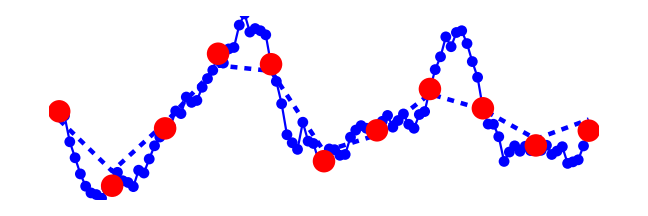

```mathematica
poly2=Show[
ListPlot[predq[[1]],PlotStyle->{RGBColor[0,0,1],Thickness[0.005],Dashed},Joined->True],
ListPlot[predq[[10]],PlotStyle->{RGBColor[0,0,1],PointSize[0.012]},Joined->True],
ListPlot[predq[[10]],PlotStyle->{RGBColor[0,0,1],PointSize[0.012]},Joined->False],
ListPlot[Transpose[{ty,predq[[10,ty]]}],PlotStyle->{RGBColor[1,0,0],PointSize[0.025]},Joined->False],
AspectRatio->1/3,
Axes->False,
PlotRange->{All,{-0.7,1.05}},Background->None
]
```

```mathematica
Export["C:\\Users\\ulzegasi\\Julia_files\\ParInf_HMC\\TeXFiles\\Figs\\poly2.png",poly2,AspectRatio->1/3,ImageSize->{1000},Background->None]
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC\TeXFiles\Figs\poly2.png

```mathematica
off=2.0
```

2.

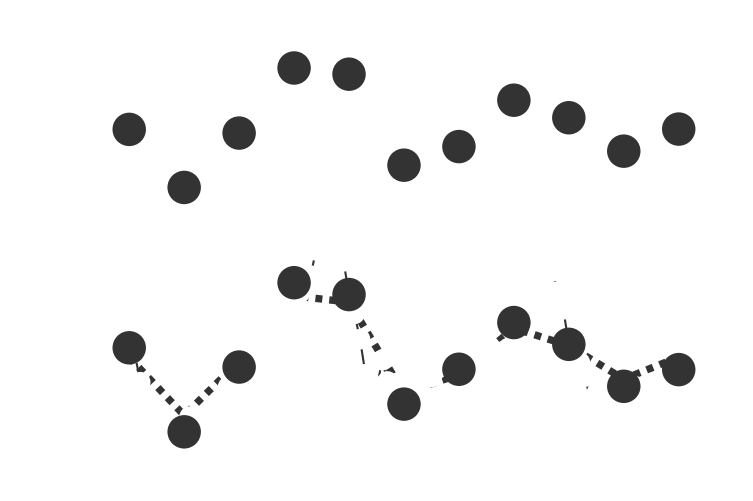

```mathematica
fullpolyfig=Show[
ListPlot[predq[[1]],PlotStyle->{RGBColor[0.2,0.2,0.2],Thickness[0.002]},Joined->True],
ListPlot[predq[[1]],PlotMarkers->Graphics[{EdgeForm[Thickness[.4]],White,Disk[]},ImageSize->14],Joined->False],
ListPlot[Transpose[{ty,predq[[1,ty]]}],PlotStyle->{RGBColor[0.2,0.2,0.2],PointSize[0.032]},Joined->False],

ListPlot[predq[[1]]-off,PlotStyle->{RGBColor[0.2,0.2,0.2],Thickness[0.007],Dashed},Joined->True],
ListPlot[predq[[10]]-off,PlotStyle->{RGBColor[0.2,0.2,0.2],Thickness[0.002]},Joined->True],
ListPlot[predq[[10]]-off,PlotMarkers->Graphics[{EdgeForm[Thickness[.4]],White,Disk[]},ImageSize->14],Joined->False],
ListPlot[Transpose[{ty,predq[[10,ty]]-off}],PlotStyle->{RGBColor[0.2,0.2,0.2],PointSize[0.032]},Joined->False],
AspectRatio->1/1.5,
Axes->False,
PlotRange->{{-10,102},{-2.8,0.8}},Background->None,AxesOrigin->{-5,1}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\poly.eps",fullpolyfig,AspectRatio->1/1.5,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\poly.eps

## “Good results” with synthetic data (figures for paper here)

## Sin rain, n = 10, j=30, nnapa = 3, dτ = 0.25

## Preliminaries

### Directories, packages, filenames

```mathematica
SetDirectory["C:/Users/ulzegasi/Julia_files/ParInf_HMC/good_results/n10 j30"]
inputdir="C:/Users/ulzegasi/Julia_files/ParInf_HMC/input_data";
Needs["CustomTicks`"]
Needs["ErrorBarPlots`"]
fname="_sinr_720_130";
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC\good_results\n10 j30

### Loading parameters and data

```mathematica
qstemp=Import["last_qs"<>fname<>".dat"];
qs=Table[qstemp[[i,1]],{i,1,Length[qstemp]}];

predy=Import["predy"<>fname<>".dat"];
predq=Import["predq"<>fname<>".dat"];

thetas=Import["thetas"<>fname<>".dat"];

energiestemp=Import["energies"<>fname<>".dat"];
energies=Table[energiestemp[[i,1]],{i,1,Length[energiestemp]}];

paramlist=Import["params"<>fname<>".dat"];

reject=Import["reject"<>fname<>".dat"];
```

```mathematica
Nd=paramlist[[Position[paramlist,"N"][[1,1]],2]];
j=paramlist[[Position[paramlist,"j"][[1,1]],2]];
n=paramlist[[Position[paramlist,"n"][[1,1]],2]];
dt=paramlist[[Position[paramlist,"dt"][[1,1]],2]];

t=Table[0,{i,1,Nd}];
t[[1]]=paramlist[[Position[paramlist,"t[1]"][[1,1]],2]];
Do[t[[i]]=t[[i-1]]+dt,{i,2,Nd}];

T=dt*(Nd-1);

nparams=paramlist[[Position[paramlist,"nparams"][[1,1]],2]];
trueK=paramlist[[Position[paramlist,"true_K"][[1,1]],2]];
trueg=paramlist[[Position[paramlist,"true_gam"][[1,1]],2]];
sigma=paramlist[[Position[paramlist,"sigma"][[1,1]],2]];
K=paramlist[[Position[paramlist,"K"][[1,1]],2]];
gamma=paramlist[[Position[paramlist,"gam"][[1,1]],2]];

nsburnin=paramlist[[Position[paramlist,"nsample_burnin"][[1,1]],2]];
nseff=paramlist[[Position[paramlist,"nsample_eff"][[1,1]],2]];
nsample=nsburnin+nseff;

Mbdyburnin=paramlist[[Position[paramlist,"m_bdy_burnin"][[1,1]],2]];
Mbdy=paramlist[[Position[paramlist,"m_bdy"][[1,1]],2]];
Mthetaburnin=paramlist[[Position[paramlist,"m_theta_burnin"][[1,1]],2]];
Mtheta={paramlist[[Position[paramlist,"m_theta_bet"][[1,1]],2]],paramlist[[Position[paramlist,"m_theta_gam"][[1,1]],2]]};
Mstageburnin=paramlist[[Position[paramlist,"m_stg_burnin"][[1,1]],2]];


Mstage=paramlist[[Position[paramlist,"m_stg"][[1,1]],2]];

dtau=paramlist[[Position[paramlist,"dtau"][[1,1]],2]];
nnapa=paramlist[[Position[paramlist,"n_napa"][[1,1]],2]];

bet=Sqrt[T*thetas[[All,2]]/thetas[[All,1]]];
```

```mathematica
ty=Round[Array[#&,n+1,{1,Nd}]];
```

```mathematica
iodata=Import["iodata"<>fname<>".dat"];
(*S=Table[iodata[[i,1]],{i,2,Nd+1}];*)
r=Table[iodata[[i,1]],{i,Nd+3,2*Nd+2}]; 
y=Table[iodata[[i,1]],{i,2*Nd+4,Length[iodata]}];

St=Import[inputdir<>"/St_n10_K50_g02_s10_sinr.dat"];
S=St[[All,1]];
tS=St[[All,2]];
```

```mathematica
uchains raw=Import["u_chains"<>fname<>".dat"];
u1=Round[uchains raw[[1,1]]];
u2=Round[uchains raw[[1,2]]];
u3=Round[uchains raw[[1,3]]];
u4=Round[uchains raw[[1,4]]];
uchains=uchains raw[[Range[2,Length[uchains raw]],All]];
```

## Plots

### Figure1 - S[t], r[t]

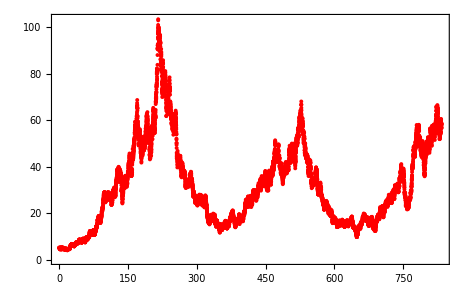

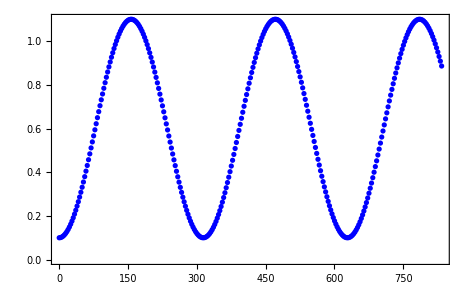

```mathematica
ListPlot[Table[{tS[[i]],S[[i]]},{i,1,Length[tS]}],PlotRange->All,PlotStyle->{Red,PointSize[0.006]},Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,16],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,200,20,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}]
ListPlot[Table[{t[[i]],r[[i]]},{i,1,Length[t]}],PlotStyle->{Blue,PointSize[0.008]},Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,16],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.5,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}]
```

### Figure 2 - S[t]/trueK, r[t], y

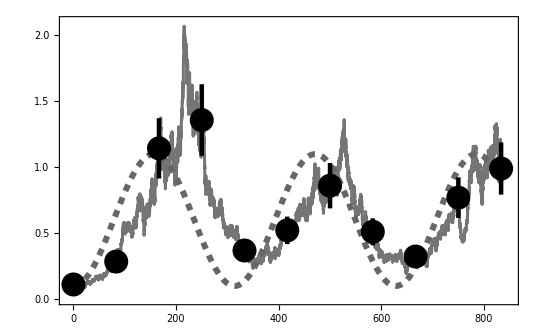

```mathematica
rSyBW=Show[

ListPlot[Table[{t[[i]],r[[i]]},{i,1,Length[t]}],PlotStyle->{Dashed,RGBColor[0.4,0.4,0.4],Thickness[0.008]},Joined->True],

ListPlot[Table[{tS[[i]],S[[i]]/trueK},{i,1,Length[tS]}],PlotStyle->{RGBColor[0.4,0.4,0.4],Thickness[0.004],Opacity[0.9]},Joined->True],

ErrorListPlot[Table[{{t[[ty[[i]]]],y[[i]]},ErrorBar[2*sigma*y[[i]]]},{i,1,Length[ty]}],PlotStyle->{RGBColor[0,0,0],PointSize[0.032],Thickness[0.006]}],

Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,28],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.5,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{{-10,850},{-0.0,2.1}}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig2.eps",rSyBW,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Fig2.eps

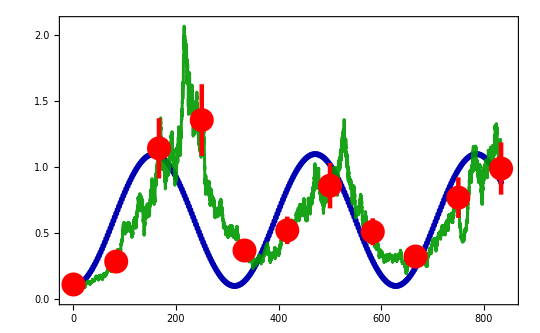

```mathematica
rSy=Show[

ListPlot[Table[{t[[i]],r[[i]]},{i,1,Length[t]}],PlotStyle->{Dotted,RGBColor[0,0,0.7],PointSize[0.008]},Joined->False],

ListPlot[Table[{tS[[i]],S[[i]]/trueK},{i,1,Length[tS]}],PlotStyle->{RGBColor[0,0.6,0],Thickness[0.004],Opacity[0.9]},Joined->True],

ErrorListPlot[Table[{{t[[ty[[i]]]],y[[i]]},ErrorBar[2*sigma*y[[i]]]},{i,1,Length[ty]}],PlotStyle->{RGBColor[1,0,0],PointSize[0.032],Thickness[0.006]}],

Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,28],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.5,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{{-10,850},{-0.0,2.1}}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Geneva 28.09.2015\\rSy.png",rSy,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Geneva 28.09.2015\rSy.png

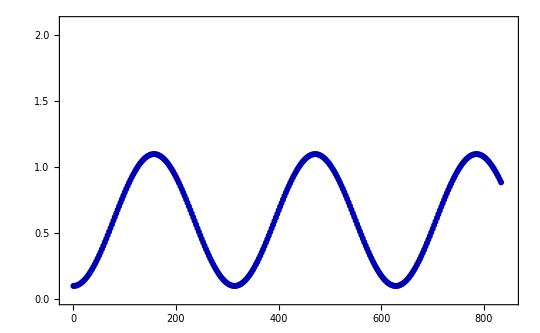

```mathematica
rain=Show[

ListPlot[Table[{t[[i]],r[[i]]},{i,1,Length[t]}],PlotStyle->{Dotted,RGBColor[0,0,0.7],PointSize[0.008]},Joined->False],

(*ListPlot[Table[{tS[[i]],S[[i]]/trueK},{i,1,Length[tS]}],PlotStyle->{RGBColor[0,0.5,0],Thickness[0.004],Opacity[0.9]},Joined->True],

ErrorListPlot[Table[{{t[[ty[[i]]]],y[[i]]},ErrorBar[2*sigma*y[[i]]]},{i,1,Length[ty]}],PlotStyle->{RGBColor[1,0,0],PointSize[0.027],Thickness[0.006]}],*)

Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,28],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.5,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{{-10,850},{-0.0,2.1}}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Geneva 28.09.2015\\rain.png",rain,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Geneva 28.09.2015\rain.png

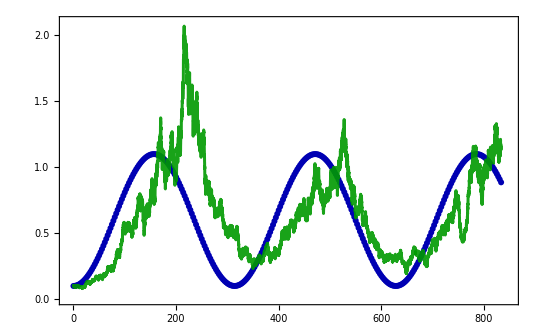

```mathematica
rS=Show[

ListPlot[Table[{t[[i]],r[[i]]},{i,1,Length[t]}],PlotStyle->{Dotted,RGBColor[0,0,0.7],PointSize[0.008]},Joined->False],

ListPlot[Table[{tS[[i]],S[[i]]/trueK},{i,1,Length[tS]}],PlotStyle->{RGBColor[0,0.6,0],Thickness[0.004],Opacity[0.9]},Joined->True],

(*ErrorListPlot[Table[{{t[[ty[[i]]]],y[[i]]},ErrorBar[2*sigma*y[[i]]]},{i,1,Length[ty]}],PlotStyle->{RGBColor[1,0,0],PointSize[0.027],Thickness[0.006]}],*)

Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,28],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.5,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{{-10,850},{-0.0,2.1}}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Geneva 28.09.2015\\rS.png",rS,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Geneva 28.09.2015\rS.png

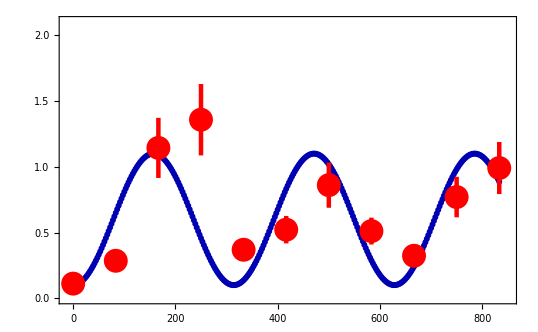

```mathematica
ry=Show[

ListPlot[Table[{t[[i]],r[[i]]},{i,1,Length[t]}],PlotStyle->{Dotted,RGBColor[0,0,0.7],PointSize[0.008]},Joined->False],

(*ListPlot[Table[{tS[[i]],S[[i]]/trueK},{i,1,Length[tS]}],PlotStyle->{RGBColor[0,0.6,0],Thickness[0.004],Opacity[0.9]},Joined->True],*)

ErrorListPlot[Table[{{t[[ty[[i]]]],y[[i]]},ErrorBar[2*sigma*y[[i]]]},{i,1,Length[ty]}],PlotStyle->{RGBColor[1,0,0],PointSize[0.032],Thickness[0.006]}],

Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,28],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.5,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{{-10,850},{-0.0,2.1}}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Geneva 28.09.2015\\ry.png",ry,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Geneva 28.09.2015\ry.png

### Figure 3 - Spaghetti plot

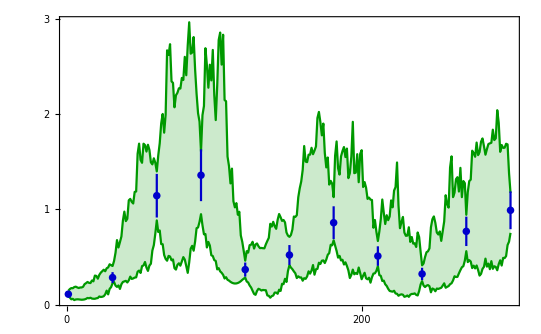

```mathematica
maxy=Table[0,{i,1,Nd}];
miny=Table[0,{i,1,Nd}];
predyT=Transpose[predy];
Do[
maxy[[i]]=Max[predyT[[i]]];
miny[[i]]=Min[predyT[[i]]];
,{i,1,Nd}];

Show[

ListPlot[{maxy,miny},Joined->True,PlotStyle->{RGBColor[0,0.6,0],RGBColor[0,0.6,0]},Filling->{1->{2}},FillingStyle->Opacity[0.2]],

ErrorListPlot[Table[{{ty[[i]],y[[i]]},ErrorBar[2*sigma*y[[i]]]},{i,1,Length[ty]}],PlotStyle->{RGBColor[0,0,0.8],PointSize[0.01]}],

Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,16],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,6,1,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},
PlotRange->{All,All}
]
```

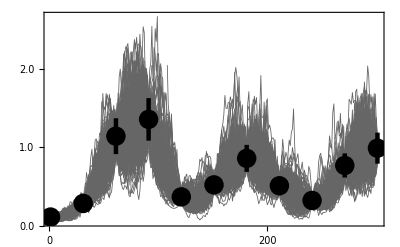

```mathematica
spaghetti=Show[

Table[ListPlot[predy[[i]],Joined->True,PlotStyle->{RGBColor[0.4,0.4,0.4],Thickness[0.0015]}],{i,1,Length[predy]}],

ErrorListPlot[Table[{{ty[[i]],y[[i]]},ErrorBar[2*sigma*y[[i]]]},{i,1,Length[ty]}],PlotStyle->{RGBColor[0,0,0],PointSize[0.035],Thickness[0.008]}],

Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,32],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,3,0.5,1,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},
PlotRange->{All,All}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig3.eps",spaghetti,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Fig3.eps

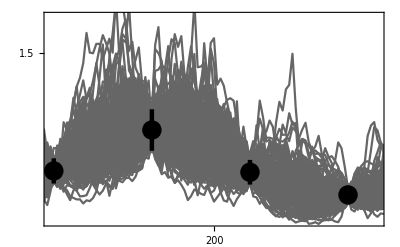

```mathematica
spaghettizoom=Show[

Table[ListPlot[predy[[i]],PlotStyle->{RGBColor[0.4,0.4,0.4],PointSize[0.008]},Joined->True],{i,1,Length[predy]}],

ErrorListPlot[Table[{{ty[[i]],y[[i]]},ErrorBar[2*sigma*y[[i]]]},{i,1,Length[ty]}],PlotStyle->{RGBColor[0,0,0],PointSize[0.035],Thickness[0.008]}],

Axes->False,Frame->True,FrameStyle->Directive[Thick,40,Black],FrameTicks->{LinTicks[0,900,20,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,6,0.5,1,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},
PlotRange->{{150,250},{0.1,1.8}}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig3zoom.eps",spaghettizoom,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Fig3zoom.eps

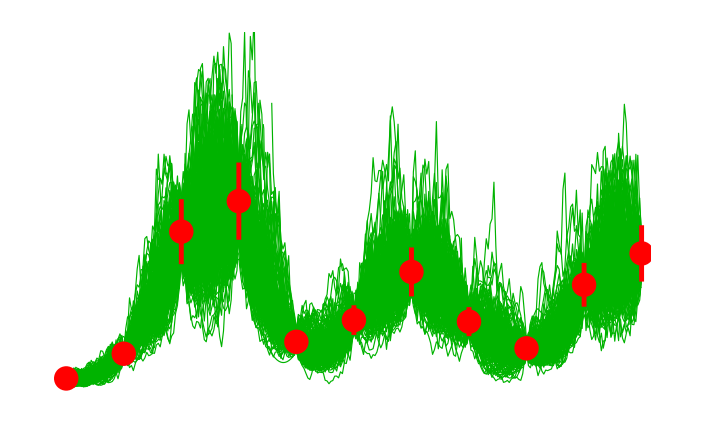

```mathematica
spaghetti color=Show[

Table[ListPlot[predy[[i]],Joined->True,PlotStyle->{RGBColor[0.0,0.7,0.0],Thickness[0.0012]}],{i,1,Length[predy]}],

ErrorListPlot[Table[{{ty[[i]],y[[i]]},ErrorBar[2*sigma*y[[i]]]},{i,1,Length[ty]}],PlotStyle->{RGBColor[1,0,0],PointSize[0.025],Thickness[0.005]}],

Axes->False,Frame->False,FrameStyle->Directive[Black,Thick,24],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,3,0.5,1,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},
PlotRange->{{0,300.},{0,2.5}}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\spaghetticolor.png",spaghetti color,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\spaghetticolor.png

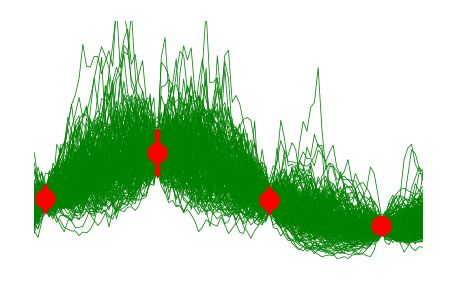

```mathematica
spaghettizoom color=Show[

Table[ListPlot[predy[[i]],Joined->True,PlotStyle->{RGBColor[0.0,0.5,0.0],Thickness[0.0012]}],{i,1,Length[predy]}],

ErrorListPlot[Table[{{ty[[i]],y[[i]]},ErrorBar[2*sigma*y[[i]]]},{i,1,Length[ty]}],PlotStyle->{RGBColor[1,0,0],PointSize[0.032],Thickness[0.008]}],

Axes->False,Frame->False,FrameStyle->Directive[Black,Thick,24],FrameTicks->{LinTicks[0,900,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,3,0.5,1,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},
PlotRange->{{150,250},{0.1,1.8}}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\spaghettizoomcolor.png",spaghettizoom color,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\spaghettizoomcolor.png

### Figure 4 - Final state and QQ plot

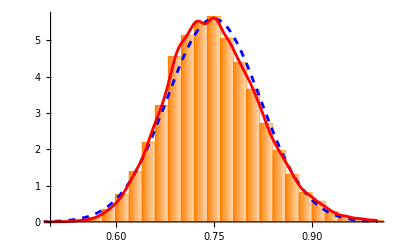

```mathematica
range=Range[(nsburnin+2),(nsample+1)];
finalstate=r[[Nd]]*Exp[bet[[range]]*qs[[range]]];
kde=SmoothKernelDistribution[finalstate];

mu=Mean[finalstate];
sig=StandardDeviation[finalstate];

Show[
Histogram[finalstate,{.02},"PDF",ChartElementFunction->"FadingRectangle",ChartStyle->Orange],

Plot[PDF[NormalDistribution[mu,sig],x],{x,0,1},Filling->False,FillingStyle->{Blue,Opacity[0.2]},

PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}],

Plot[PDF[kde,x],{x,0,1},PlotStyle->{Red,Thickness[0.005]},PlotRange->All],

PlotRange->{{0.50,1.000},All},AxesOrigin->{0.5,0},

LabelStyle->{FontFamily->"Helvetica",16,RGBColor[0.,0.,0.]}

]
```

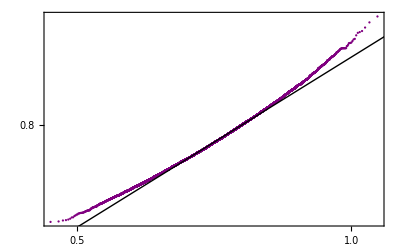

```mathematica
QuantilePlot[finalstate,PlotStyle->Directive[PointSize[0.004],Purple],Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,16],FrameTicks->{LinTicks[0,2,0.1,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.1,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}]
```

### Figure 5 - Markov chains for the parameters

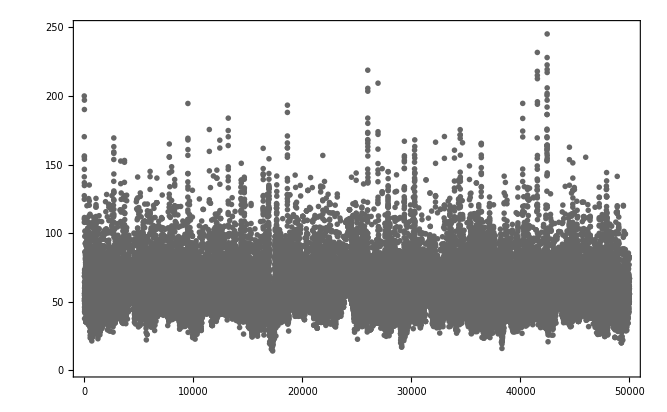

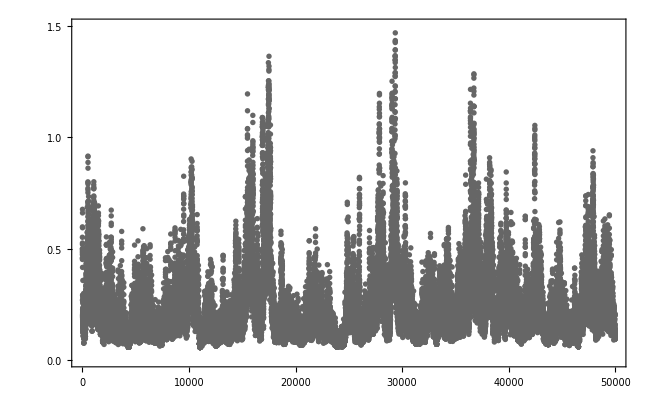

```mathematica
chainK=Show[ListPlot[thetas[[All,1]],PlotStyle->{RGBColor[0.4,0.4,0.4],PointSize[0.006]},Joined->False],Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,36],FrameTicks->{LinTicks[0,50000,10000,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,250,50,1,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{0,250}}]

chainG=Show[ListPlot[thetas[[All,2]],PlotStyle->{RGBColor[0.4,0.4,0.4],PointSize[0.006]},Joined->False],Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,36],FrameTicks->{LinTicks[0,50000,10000,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.5,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{0,1.5}}]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig4.eps",chainK,ImageSize->{1000},Background->None]
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig5.eps",chainG,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Fig4.eps

\\eaw-homedirs\ulzegasi$\Desktop\Fig5.eps

### Figure 6 - Evolution in K-γ space

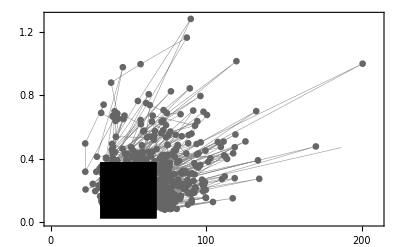

```mathematica
grid=Round[Array[#&,1000,{1,Length[thetas]}]];
grid2=grid[[Range[Length[grid]-50,Length[grid]-1]]];

chainKG=Show[
ListPlot[Transpose[{thetas[[grid,1]],thetas[[grid,2]]}],PlotStyle->{RGBColor[0.4,0.4,0.4],PointSize[0.012]},Joined->False],
ListPlot[Transpose[{thetas[[grid,1]],thetas[[grid,2]]}],PlotStyle->{RGBColor[0.4,0.4,0.4],Thickness[0.001],Opacity[0.7]},Joined->True,PlotRange->All],

ListPlot[{{thetas[[1,1]],thetas[[1,2]]}},PlotMarkers->Graphics[{EdgeForm[Thickness[.4]],White,Disk[]},ImageSize->36],Joined->False],
(*ListPlot[{{thetas[[Last[grid],1]],thetas[[Last[grid],2]]}},PlotStyle->{RGBColor[1,0,0],PointSize[0.02]},Joined->False],*)

(*ListPlot[Transpose[{thetas[[grid2,1]],thetas[[grid2,2]]}],PlotStyle->{Orange,PointSize[0.012]},Joined->False],*)

ListPlot[{{trueK,trueg}},PlotMarkers->{"■",58},PlotStyle->{RGBColor[0,0,0]},Joined->False],

Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,38],FrameTicks->{LinTicks[0,250,50,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},

PlotRange->{{0,210},{0,1.3}}
]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig6.eps",chainKG,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Fig6.eps

### Figure 7 - Parameters PDF

```mathematica
range=Range[(nsburnin+2),(nsample+1)];
ks=thetas[[range,1]];
gs=thetas[[range,2]];
kdeK=SmoothKernelDistribution[ks];
kdeG=SmoothKernelDistribution[gs];

muK=Mean[ks];
sigK=StandardDeviation[ks];

muG=Mean[gs];
sigG=StandardDeviation[gs];
```

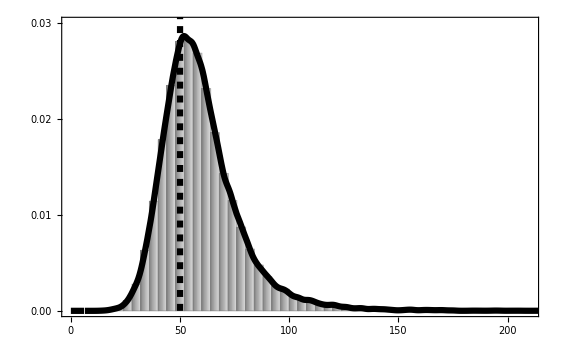

```mathematica
pdfK=Show[
Histogram[ks,{4},"PDF",ChartElementFunction->"FadingRectangle",ChartStyle->Gray],
(*Plot[PDF[NormalDistribution[muK,sigK],x],{x,0,600},Filling->False,FillingStyle->{Blue,Opacity[0.2]},

PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}],*)

Plot[PDF[kdeK,x],{x,0,600},PlotStyle->{Black,Thickness[0.008]},PlotRange->All],
Graphics[{Thickness[0.008],Dashed,Black,Line[{{trueK,0},{trueK,0.0315}}]}],

AxesOrigin->{0,0},
Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,46],FrameTicks->{LinTicks[0,250,50,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,0.03,0.01,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},

PlotRange->{{0,210},{0,0.03}}

]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig7_K.eps",pdfK,Background->None]
```

Export::noopen: Cannot open "\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig7_K.eps".

$Failed

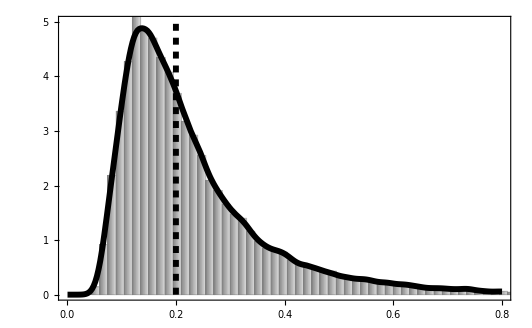

```mathematica
pdfG=Show[
Histogram[gs,{0.015},"PDF",ChartElementFunction->"FadingRectangle",ChartStyle->Gray],

(*Plot[PDF[NormalDistribution[muG,sigG],x],{x,0,0.6},Filling->False,FillingStyle->{Blue,Opacity[0.2]},

PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}],*)

Plot[PDF[kdeG,x],{x,0,0.8},PlotStyle->{Black,Thickness[0.008]},PlotRange->All],
Graphics[{Thickness[0.008],Dashed,Black,Line[{{trueg,0},{trueg,5.1}}]}],
AxesOrigin->{0,0},

Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,46],FrameTicks->{LinTicks[0,0.8,0.2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,5,1,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},

PlotRange->{{0,0.8},{0,5}}

]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig7_gamma.eps",pdfG,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Fig7_gamma.eps

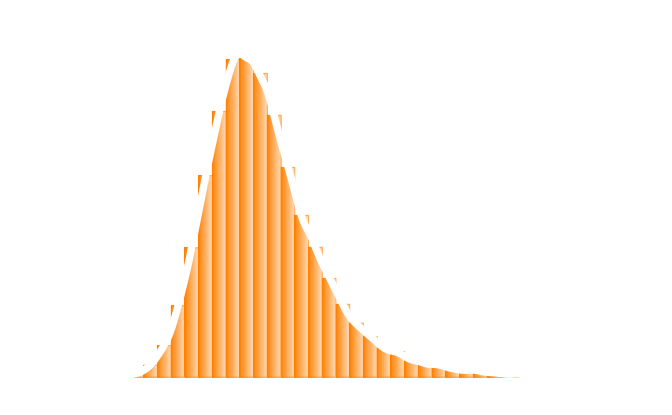

```mathematica
pdfK color=Show[
Histogram[ks,{4},"PDF",ChartElementFunction->"FadingRectangle",ChartStyle->Orange],
(*Plot[PDF[NormalDistribution[muK,sigK],x],{x,0,600},Filling->False,FillingStyle->{Blue,Opacity[0.2]},

PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}],*)

Plot[PDF[kdeK,x],{x,0,600},PlotStyle->{White,Thickness[0.008]},PlotRange->All],

AxesOrigin->{0,0},
Axes->False,Frame->False,FrameStyle->Directive[Black,Thick,46],FrameTicks->{LinTicks[0,250,50,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,0.03,0.01,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},

PlotRange->{{0,160},{0,0.03}}

]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\pdfKcolor.png",pdfK color,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\pdfKcolor.png

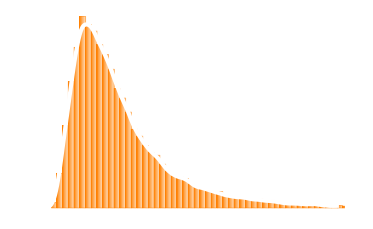

```mathematica
pdfG color=Show[
Histogram[gs,{0.015},"PDF",ChartElementFunction->"FadingRectangle",ChartStyle->Orange],

(*Plot[PDF[NormalDistribution[muG,sigG],x],{x,0,0.6},Filling->False,FillingStyle->{Blue,Opacity[0.2]},

PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}],*)

Plot[PDF[kdeG,x],{x,0,0.8},PlotStyle->{White,Thickness[0.008]},PlotRange->All],
AxesOrigin->{0,0},

Axes->False,Frame->False,FrameStyle->Directive[Black,Thick,46],FrameTicks->{LinTicks[0,0.8,0.2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,5,1,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},

PlotRange->{{0,0.8},{0,5}}

]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\pdfGcolor.png",pdfG color,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\pdfGcolor.png

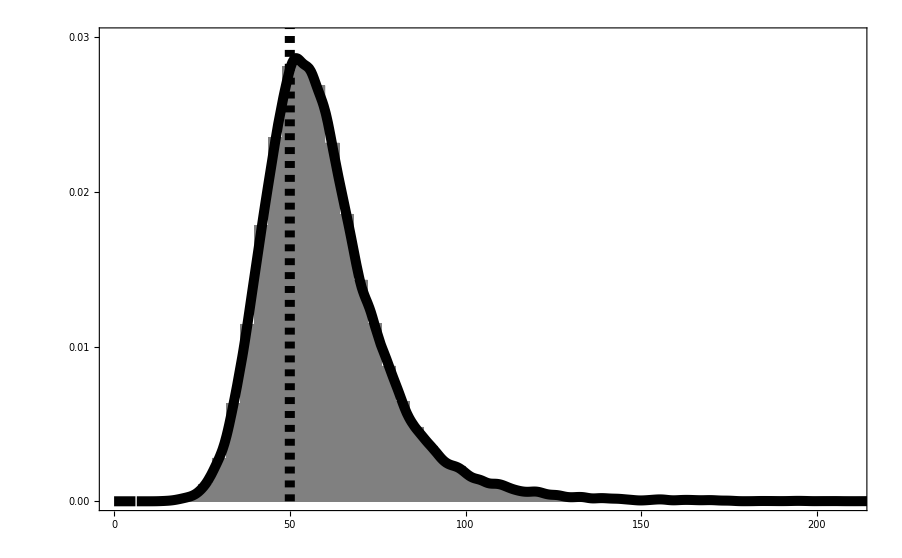

```mathematica
pdfK=Show[
Histogram[ks,{4},"PDF",ChartStyle->Gray],
(*Plot[PDF[NormalDistribution[muK,sigK],x],{x,0,600},Filling->False,FillingStyle->{Blue,Opacity[0.2]},

PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}],*)

Plot[PDF[kdeK,x],{x,0,600},PlotStyle->{Black,Thickness[0.008]},PlotRange->All],
Graphics[{Thickness[0.008],Dashed,Black,Line[{{trueK,0},{trueK,0.0315}}]}],

AxesOrigin->{0,0},
Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,46],FrameTicks->{LinTicks[0,250,50,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,0.03,0.01,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},

PlotRange->{{0,210},{0,0.03}}

]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig7_K.eps",pdfK,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Fig7_K.eps

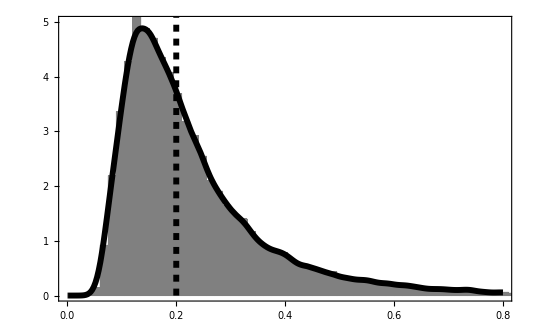

```mathematica
pdfG=Show[
Histogram[gs,{0.015},"PDF",ChartStyle->Gray],

(*Plot[PDF[NormalDistribution[muG,sigG],x],{x,0,0.6},Filling->False,FillingStyle->{Blue,Opacity[0.2]},

PlotRange->All,PlotStyle->{Blue,Dashed,Thickness[0.005]}],*)

Plot[PDF[kdeG,x],{x,0,0.8},PlotStyle->{Black,Thickness[0.008]},PlotRange->All],
Graphics[{Thickness[0.008],Dashed,Black,Line[{{trueg,0},{trueg,5.1}}]}],
AxesOrigin->{0,0},

Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,46],FrameTicks->{LinTicks[0,0.8,0.2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,5,1,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},

PlotRange->{{0,0.8},{0,5}}

]
```

```mathematica
Export["\\\\eaw-homedirs\\ulzegasi$\\Desktop\\Fig7_gamma.eps",pdfG,ImageSize->{1000},Background->None]
```

\\eaw-homedirs\ulzegasi$\Desktop\Fig7_gamma.eps

### Figure 8 - Energies

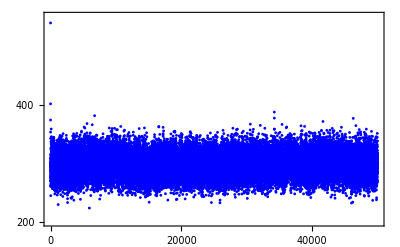

```mathematica
ListPlot[energies,PlotStyle->{Blue,PointSize[0.005]},Joined->False,

Axes->False,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,50000,10000,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,1000,100,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},

PlotRange->{All,{200,550}}]
```

### Figure 9 - Markov chains for the u modes

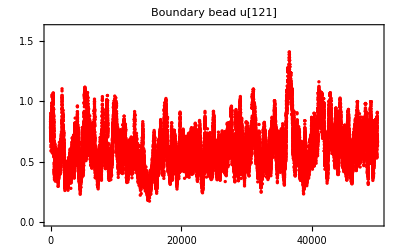

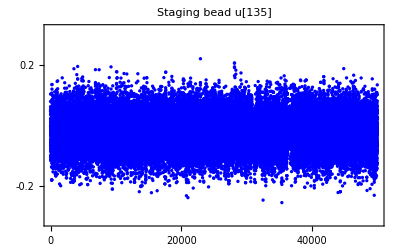

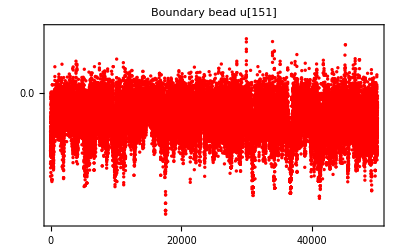

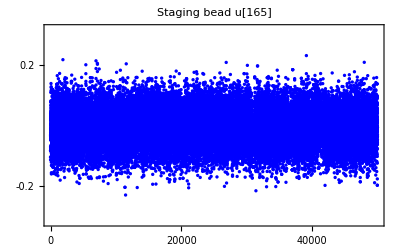

```mathematica
ListPlot[uchains[[All,1]],PlotStyle->{RGBColor[1,0,0],PointSize[0.006]},Joined->False,Axes->False,Frame->True,PlotLabel->"Boundary bead u["<>ToString[u1]<>"]",FrameStyle->Directive[Black,Thick,16],FrameTicks->{LinTicks[0,50000,10000,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.5,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{0,1.6}}]

ListPlot[uchains[[All,2]],PlotStyle->{Blue,PointSize[0.006]},Joined->False,Axes->False,Frame->True,PlotLabel->"Staging bead u["<>ToString[u2]<>"]",FrameStyle->Directive[Black,Thick,16],FrameTicks->{LinTicks[0,50000,10000,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-1,1,0.2,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{-0.32,0.32}}]

ListPlot[uchains[[All,3]],PlotStyle->{RGBColor[1,0,0],PointSize[0.006]},Joined->False,Axes->False,Frame->True,PlotLabel->"Boundary bead u["<>ToString[u3]<>"]",FrameStyle->Directive[Black,Thick,16],FrameTicks->{LinTicks[0,50000,10000,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,2,0.5,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{-0.4,0.2}}]

ListPlot[uchains[[All,4]],PlotStyle->{Blue,PointSize[0.006]},Joined->False,Axes->False,Frame->True,PlotLabel->"Staging bead u["<>ToString[u4]<>"]",FrameStyle->Directive[Black,Thick,16],FrameTicks->{LinTicks[0,50000,10000,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-1,1,0.2,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{-0.32,0.32}}]
```

### Figure 10 - Markov chains for the u modes

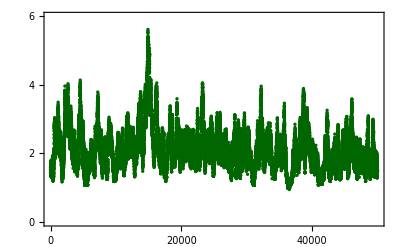

```mathematica
ListPlot[bet,PlotStyle->{RGBColor[0,0.4,0],PointSize[0.006]},Joined->False,Axes->False,Frame->True,FrameStyle->Directive[Black,Thick,16],FrameTicks->{LinTicks[0,50000,10000,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,6,1,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{0,6}}]
```